Дебиты несовершенных скважин:

Гиринского: 61.4554

Маскега: 36.8853

Козени: 36.8853

Чарного: 3.26519

Дебиты горизонтальных скважин:

Борисова: 128.704

Джоши: 125.752

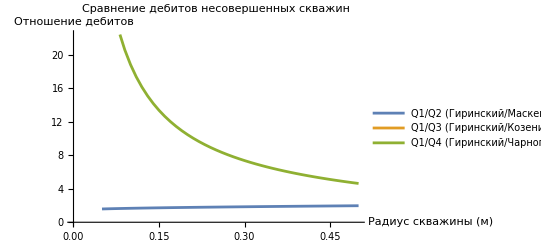

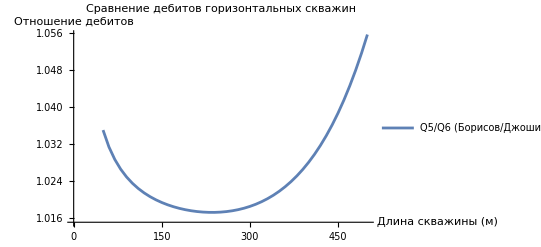

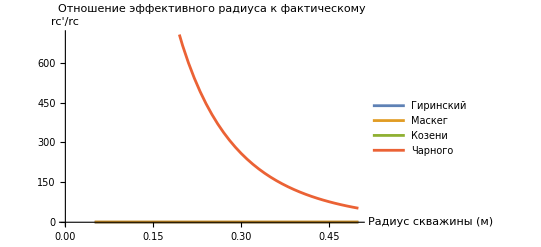

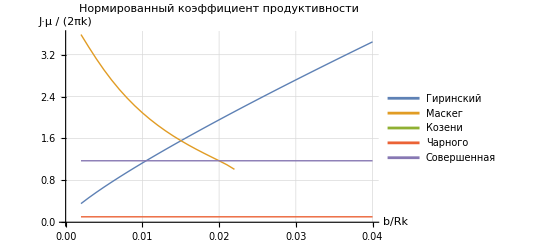

```mathematica
(*Определение констант и параметров*)k=0.1 (*проницаемость,Д*);
b=10 (*толщина пласта,м*);
h=10 (*толщина вскрытой части пласта,м*);
mu=1 (*вязкость,сПз*);
pk=100 (*давление на контуре,атм*);
pc=50 (*давление на забое,атм*);
rc=0.1 (*радиус скважины,м*);
Rk=500 (*радиус контура питания,м*);
Ro = 1;
l=100 (*длина горизонтальной скважины,м*);
deltaP=pk-pc;

(*Вспомогательные функции*)
phi[x_]:=Log[Gamma[0.875*x]*Gamma[0.125*x]/(Gamma[1-0.875*x]*Gamma[1-0.125*x])];
a[lVal_,RkVal_]:=lVal*Sqrt[0.5+Sqrt[0.25+(RkVal/lVal)^4]];

(*Формулы для несовершенных скважин*)

(*1. Формула Гиринского*)
Q1[bVal_,rcVal_]:=(2*Pi*k*bVal/mu)*(pk-pc)/Log[1.66*bVal/rcVal];

(*2. Формула Маскета*)
xi[hVal_,rcVal_,bVal_]:=(1/(2*hVal/bVal))*(2*Log[4*hVal/rcVal]-phi[bVal/hVal])-Log[4*hVal/Rk];
Q2[hVal_,rcVal_,bVal_]:=(2*Pi*k*hVal/mu)*(pk-pc)/xi[hVal,rcVal,bVal];

(*3. Формула Козени*)
Q3[hVal_,rcVal_, bVal_]:=(2*Pi*k*bVal/mu)*(pk-pc)/Log[Rk/rcVal]*(1+7*Sqrt[rcVal/(2*bVal)]*Cos[(Pi*bVal)/(2*hVal)]);

(*4. Формула Чарного*)
Q4[hVal_,rcVal_]:=(2*Pi*k*hVal/mu)*(pk-pc)/(Log[Rk/Ro]+hVal/rcVal-hVal/Ro);

(*Формулы для горизонтальных скважин*)

(*5. Формула Борисова*)
Q5[hVal_,rcVal_,lVal_]:=(2*Pi*k*hVal/mu)*deltaP/(Log[2*Rk/lVal]+(hVal/(2*lVal))*Log[hVal/(2*Pi*rcVal)]);

(*6. Формула Джоши*)
Q6[hVal_,rcVal_,lVal_]:=Module[{aVal=a[lVal,Rk]},(2*Pi*k*hVal/mu)*deltaP/(Log[(aVal+Sqrt[aVal^2-lVal^2])/lVal]+(hVal/(2*lVal))*Log[hVal/(2*rcVal)])];

(*Анализ несовершенных скважин*)
Print["Дебиты несовершенных скважин:"];
Print["Гиринского: ",Q1[b,rc]];
Print["Маскега: ",Q2[h,rc,b]];
Print["Козени: ",Q3[h,rc, b]];
Print["Чарного: ",Q4[h,rc]];

(*Анализ горизонтальных скважин*)
Print["\nДебиты горизонтальных скважин:"];
Print["Борисова: ",Q5[h,rc,l]];
Print["Джоши: ",Q6[h,rc,l]];

(*Построение графиков отношений дебитов*)

(*Для несовершенных скважин*)
rcValues=Table[rcVal,{rcVal,0.05,0.5,0.01}];
ratios1=Table[Q1[b,rcVal]/Q2[h,rcVal,b],{rcVal,rcValues}];
ratios2=Table[Q1[b,rcVal]/Q3[h,rcVal],{rcVal,rcValues}];
ratios3=Table[Q1[b,rcVal]/Q4[h,rcVal],{rcVal,rcValues}];

Plot1=ListLinePlot[{Transpose[{rcValues,ratios1}],Transpose[{rcValues,ratios2}],Transpose[{rcValues,ratios3}]},PlotLegends->{"Q1/Q2 (Гиринский/Маскег)","Q1/Q3 (Гиринский/Козени)","Q1/Q4 (Гиринский/Чарного)"},AxesLabel->{"Радиус скважины (м)","Отношение дебитов"},PlotLabel->"Сравнение дебитов несовершенных скважин"];

(*Для горизонтальных скважин*)
lValues=Table[lVal,{lVal,50,500,10}];
ratiosH=Table[Q5[h,rc,lVal]/Q6[h,rc,lVal],{lVal,lValues}];

Plot2=ListLinePlot[Transpose[{lValues,ratiosH}],PlotLegends->{"Q5/Q6 (Борисов/Джоши)"},AxesLabel->{"Длина скважины (м)","Отношение дебитов"},PlotLabel->"Сравнение дебитов горизонтальных скважин"];

(*Расчет эффективного радиуса rc'*)

(*Для несовершенной скважины (сравниваем с формулой совершенной скважины)*)
perfectQ[hVal_,rcVal_]:=(2*Pi*k*hVal/mu)*(pk-pc)/Log[Rk/rcVal];

rcPrime1[rcVal_]:=rcVal*Exp[(perfectQ[h,rcVal]-Q1[b,rcVal])*Log[Rk/rcVal]/perfectQ[h,rcVal]];
rcPrime2[rcVal_]:=rcVal*Exp[(perfectQ[h,rcVal]-Q2[h,rcVal,b])*Log[Rk/rcVal]/perfectQ[h,rcVal]];
rcPrime3[rcVal_]:=rcVal*Exp[(perfectQ[h,rcVal]-Q3[h,rcVal])*Log[Rk/rcVal]/perfectQ[h,rcVal]];
rcPrime4[rcVal_]:=rcVal*Exp[(perfectQ[h,rcVal]-Q4[h,rcVal])*Log[Rk/rcVal]/perfectQ[h,rcVal]];

rcPrimeRatios1=Table[rcPrime1[rcVal]/rcVal,{rcVal,rcValues}];
rcPrimeRatios2=Table[rcPrime2[rcVal]/rcVal,{rcVal,rcValues}];
rcPrimeRatios3=Table[rcPrime3[rcVal]/rcVal,{rcVal,rcValues}];
rcPrimeRatios4=Table[rcPrime4[rcVal]/rcVal,{rcVal,rcValues}];

Plot3=ListLinePlot[{Transpose[{rcValues,rcPrimeRatios1}],Transpose[{rcValues,rcPrimeRatios2}],Transpose[{rcValues,rcPrimeRatios3}],Transpose[{rcValues,rcPrimeRatios4}]},PlotLegends->{"Гиринский","Маскег","Козени","Чарного"},AxesLabel->{"Радиус скважины (м)","rc'/rc"},PlotLabel->"Отношение эффективного радиуса к фактическому"];

(*График нормированного коэффициента продуктивности*)bRange=Table[bVal,{bVal,1,20,0.5}];

(*Перерасчет всех формул с переменным b*)
jNorm1=Table[{bVal/Rk,Q1[bVal,rc]*mu/(2*Pi*k*deltaP)},{bVal,bRange}];
jNorm2=Table[{bVal/Rk,Q2[h,rc,bVal]*mu/(2*Pi*k*deltaP)},{bVal,bRange}];
jNorm3=Table[{bVal/Rk,Q3[h,rc]*mu/(2*Pi*k*deltaP)},{bVal,bRange}];
jNorm4=Table[{bVal/Rk,Q4[h,rc]*mu/(2*Pi*k*deltaP)},{bVal,bRange}];
jNormPerfect=Table[{bVal/Rk,perfectQ[h,rc]*mu/(2*Pi*k*deltaP)},{bVal,bRange}];

(*Построение графика*)
PlotProductivity=ListLinePlot[{jNorm1,jNorm2,jNorm3,jNorm4,jNormPerfect},PlotLegends->{"Гиринский","Маскег","Козени","Чарного","Совершенная"},AxesLabel->{"b/Rk","J·μ / (2πk)"},PlotLabel->"Нормированный коэффициент продуктивности",PlotStyle->Thick,GridLines->Automatic];

(*Отображение всех графиков*)
Print[Plot1];
Print[Plot2];
Print[Plot3];
Print[PlotProductivity]
```